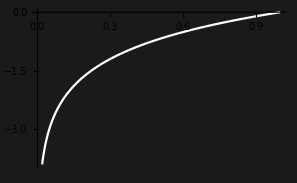

```mathematica
Plot[Log[x],{x,0.001,1},Background->GrayLevel[0.1],PlotStyle->White,AxesStyle->LightGray]
```

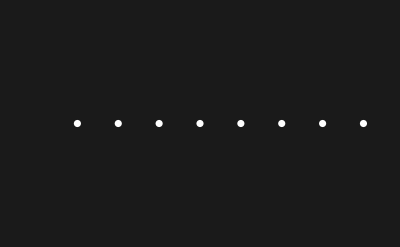

```mathematica
ListPlot[{1/8,1/8,1/8, 1/8, 1/8, 1/8, 1/8, 1/8},Background->GrayLevel[0.1],PlotStyle->White,AxesStyle->LightGray, Axes->False]
```

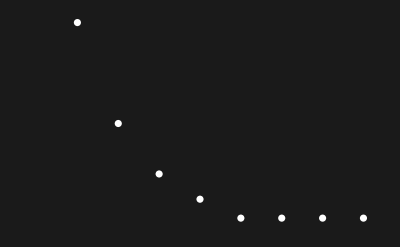

```mathematica
ListPlot[{1/2,1/4,1/8, 1/16, 1/64, 1/64, 1/64, 1/64},Background->GrayLevel[0.1],PlotStyle->White,AxesStyle->LightGray, Axes->False]
```

```mathematica
MultinormalDistribution
```

```mathematica
gaussianPlot=GraphicsRow[ParallelTable[Plot3D[PDF[MultinormalDistribution[{0,0},{{1,ρ 2},{ρ 2,1}}],{x,y}],{x,-3,3},{y,-3,3},PlotRange->All,MeshFunctions->{#3&},MeshShading->{None,Red,None,Yellow},PlotPoints->25],{ρ,{0,0.4}}],ImageSize->600,Background->GrayLevel[0.1],AxesStyle->White,PlotRangePadding->None,ImagePadding->None]
```

-Graphics-

```mathematica
Export["/Users/scherf/Dropbox/work/teaching/2017-Machine-Learning-Neuroscience/lectures/03-Probability/img/2d-gaussians.png",gaussianPlot,ImageResolution->200]
```

/Users/scherf/Dropbox/work/teaching/2017-Machine-Learning-Neuroscience/lectures/03-Probability/img/2d-gaussians.png